```mathematica
deqs=b1==α'[t]-2α[t]β'[t]+4 α[t]^2 ⅇ^(-2β[t])γ'[t]&&b2==β'[t]-4α[t] ⅇ^(-2β[t])γ'[t]&&b3==ⅇ^(-2β[t])γ'[t];
prul={b1->Im[z] (m Ω)/2,b2->-Re[z],b3->(-Im[z])/(2m Ω)};
bcon=α[0]==0&&β[0]==0&&γ[0]==0;
```

```mathematica
deqr=Solve[deqs,{α'[t],β'[t],γ'[t]}]/.Rule->Equal//Flatten
```

{α'[t]==b1+2 b2 α[t]+4 b3 α[t]^2,β'[t]==b2+4 b3 α[t],γ'[t]==b3 ⅇ^(2 β[t])}

```mathematica
deqrS=deqr/.prul
```

{α'[t]==1/2 m Ω Im[z]-2 Re[z] α[t]-(2 Im[z] α[t]^2)/(m Ω),β'[t]==-Re[z]-(2 Im[z] α[t])/(m Ω),γ'[t]==-(ⅇ^(2 β[t]) Im[z])/(2 m Ω)}

```mathematica
FullSimplify[deqrS[[1]]/.{α'[t]->t'[α]^-1,α[t]->α}]
FullSimplify[DSolve[%,t[α],α][[1]]/.{Im[z]->r Sin[ϕ],Re[z]->r Cos[ϕ]},Assumptions->r>0]
Solve[0==t[α]/.%/.α->0,C[1]][[1]]
Simplify[InverseFunction[Function[α,Evaluate[t[α]/.%%/.%]]][t]//TrigExpand]
solα=α[t]->Simplify[%,Assumptions->Re[r t+ArcTanh[Cos[ϕ]]]>0&&-π/2≤Im[r t+ArcTanh[Cos[ϕ]]]<π/2]
```

(-(4 α^2)/(m Ω)+m Ω) Im[z]==4 α Re[z]+2/t'[α]

{t[α]→ArcTanh[Cos[ϕ]+(2 α Sin[ϕ])/(m Ω)]/r+C[1]}

{C[1]→-ArcTanh[Cos[ϕ]]/r}

ConditionalExpression[(m Ω Sin[ϕ] Sinh[r t])/(2 Cosh[r t]+2 Cos[ϕ] Sinh[r t]),(Re[r t+ArcTanh[Cos[ϕ]]]<0&&-π/2<Im[r t+ArcTanh[Cos[ϕ]]]≤π/2)||(Re[r t+ArcTanh[Cos[ϕ]]]==0&&-π/2<Im[r t+ArcTanh[Cos[ϕ]]]<π/2)||(Re[r t+ArcTanh[Cos[ϕ]]]>0&&-π/2≤Im[r t+ArcTanh[Cos[ϕ]]]<π/2)]

α[t]→(m Ω Sin[ϕ] Sinh[r t])/(2 Cosh[r t]+2 Cos[ϕ] Sinh[r t])

```mathematica
α[t]/.solα/.t->0//FullSimplify
FullSimplify[α'[t]/.ToRules[deqrS[[1]]]/.{Im[z]->r Sin[ϕ],Re[z]->r Cos[ϕ]}/.solα,Assumptions->r>0]
D[α[t]/.solα,t]//FullSimplify
%==%%
```

0

(m r Ω Sin[ϕ])/(2 (Cosh[r t]+Cos[ϕ] Sinh[r t])^2)

(m r Ω Sin[ϕ])/(2 (Cosh[r t]+Cos[ϕ] Sinh[r t])^2)

True

```mathematica
DSolve[deqrS[[2]]/.{Im[z]->r Sin[ϕ],Re[z]->r Cos[ϕ]}/.solα,β[t],t][[1]]
Solve[0==β[t]/.%/.t->0,C[1]][[1]]
solβ=FullSimplify[%%/.%][[1]]
```

{β[t]→C[1]-Log[Cosh[r t]+Cos[ϕ] Sinh[r t]]}

{C[1]→0}

β[t]→-Log[Cosh[r t]+Cos[ϕ] Sinh[r t]]

```mathematica
β[t]/.solβ/.t->0//FullSimplify
FullSimplify[β'[t]/.ToRules[deqrS[[2]]]/.{Im[z]->r Sin[ϕ],Re[z]->r Cos[ϕ]}/.solα,Assumptions->r>0]
D[β[t]/.solβ,t]//FullSimplify
%==%%
```

0

-(r (Cos[ϕ] Cosh[r t]+Sinh[r t]))/(Cosh[r t]+Cos[ϕ] Sinh[r t])

-(r (Cos[ϕ] Cosh[r t]+Sinh[r t]))/(Cosh[r t]+Cos[ϕ] Sinh[r t])

True

```mathematica
DSolve[deqrS[[3]]/.{Im[z]->r Sin[ϕ],Re[z]->r Cos[ϕ]}/.solβ,γ[t],t][[1]]
Solve[0==γ[t]/.%/.t->0,C[1]][[1]]
solγ=Simplify[%%/.%][[1]]
```

{γ[t]→C[1]-(r Sin[ϕ] Sinh[r t])/(2 m Ω (r Cosh[r t]+r Cos[ϕ] Sinh[r t]))}

{C[1]→0}

γ[t]→-(Sin[ϕ] Sinh[r t])/(2 m Ω Cosh[r t]+2 m Ω Cos[ϕ] Sinh[r t])

```mathematica
γ[t]/.solγ/.t->0//FullSimplify
Simplify[γ'[t]/.ToRules[deqrS[[3]]]/.{Im[z]->r Sin[ϕ],Re[z]->r Cos[ϕ]}/.solγ/.solβ,Assumptions->r>0]
D[γ[t]/.solγ,t]//Simplify
%==%%
```

0

-(r Sin[ϕ])/(2 m Ω (Cosh[r t]+Cos[ϕ] Sinh[r t])^2)

-(r Sin[ϕ])/(2 m Ω (Cosh[r t]+Cos[ϕ] Sinh[r t])^2)

True

```mathematica
Map[#[t]&,{α,β,γ}]/.{solα,solβ,solγ}/.t->1
MapThread[#1->#2&,{{α,β,γ},%}]
solAll=FullSimplify[(%/.Cosh[r]->λ-Cos[ϕ]Sinh[r])/.{Sin[ϕ] Sinh[r]->σ λ}]
Cosh[r]+Cos[ϕ] Sinh[r]==ⅇ^r Cos[ϕ/2]^2+ⅇ^-r Sin[ϕ/2]^2//FullSimplify
```

{(m Ω Sin[ϕ] Sinh[r])/(2 Cosh[r]+2 Cos[ϕ] Sinh[r]),-Log[Cosh[r]+Cos[ϕ] Sinh[r]],-(Sin[ϕ] Sinh[r])/(2 m Ω Cosh[r]+2 m Ω Cos[ϕ] Sinh[r])}

{α→(m Ω Sin[ϕ] Sinh[r])/(2 Cosh[r]+2 Cos[ϕ] Sinh[r]),β→-Log[Cosh[r]+Cos[ϕ] Sinh[r]],γ→-(Sin[ϕ] Sinh[r])/(2 m Ω Cosh[r]+2 m Ω Cos[ϕ] Sinh[r])}

{α→(m σ Ω)/2,β→-Log[λ],γ→-σ/(2 m Ω)}

True

```mathematica
(*θ=ϕ/2*)
FullSimplify[(Sin[2θ]Sinh[r])/(Cosh[r]+Cos[2θ]Sinh[r])]
```

1/(Cot[2 θ]+Coth[r] Csc[2 θ])

```mathematica
Simplify[Integrate[(-4π ⅈ γ)^(-1/2)ⅇ^(-ⅈ(x -y)^2/(4γ))((m Ω)/π)^(1/4)ⅇ^(-(m Ω)/2 y^2),{y,-∞,∞},Assumptions->m>0&&Ω>0&&Im[γ]==0&&Im[1/γ]==0],Assumptions->m>0&&Ω>0&&Im[γ]==0&&Im[1/γ]==0]
ⅇ^(ⅈ α x^2)ⅇ^(β/2)(%/.x->x ⅇ^β)//Simplify
Simplify[%/.solAll,Assumptions->λ>0&&m>0&&Ω>0]
Simplify[Limit[%,σ->0],Assumptions->λ>0&&m>0&&Ω>0]
Simplify[%%/.{λ->S,σ->2κ} ,Assumptions->S>0&&m>0&&Ω>0]
```

(ⅇ^(-(ⅈ m x^2 Ω)/(2 ⅈ+4 m γ Ω)) (m Ω)^(1/4))/(π^(1/4) √(-ⅈ γ) √(ⅈ/γ+2 m Ω))

(ⅇ^(β/2+x^2 (ⅈ α+(ⅇ^(2 β) m Ω)/(-2+4 ⅈ m γ Ω))) (m Ω)^(1/4))/(π^(1/4) √(-ⅈ γ) √(ⅈ/γ+2 m Ω))

(ⅇ^(m x^2 (Ω/(λ^2 (-2-2 ⅈ σ))+(ⅈ σ Ω)/2)) (m Ω)^(1/4))/(π^(1/4) √(ⅈ λ σ) √((-ⅈ+σ)/σ))

(ⅇ^(-(m x^2 Ω)/(2 λ^2)) (m Ω)^(1/4))/(π^(1/4) √λ)

(ⅇ^(m x^2 (Ω/(S^2 (-2-4 ⅈ κ))+ⅈ κ Ω)) (m Ω)^(1/4))/(π^(1/4) √(2-ⅈ/κ) √(ⅈ S κ))

```mathematica
(*In the lieterature*)
Integrate[1/(4π γ)^(1/2)ⅇ^(-(y-x)^2/(4γ))((m Ω)/π)^(1/4)ⅇ^(-(m Ω)/2 y^2) ,{y,-∞,∞},Assumptions->Re[1/γ]==0&&m>0&&Ω>0]
Simplify[λ^(-1/2)ⅇ^(α x^2)(%/.x->x ⅇ^β)/.{α->ⅈ(m Ω)/2 σ,β->-Log[λ],γ->ⅈ 1/(2m Ω)σ},Assumptions->m>0&&Ω>0&&λ>0]
```

(ⅇ^(-(m x^2 Ω)/(2+4 m γ Ω)) (m Ω)^(1/4))/(π^(1/4) √γ √(1/γ+2 m Ω))

(ⅇ^(-1/2 m x^2 (2/(λ^2 (2+2 ⅈ σ))-ⅈ σ) Ω) (m Ω)^(1/4))/(π^(1/4) √(ⅈ λ σ) √((-ⅈ+σ)/σ))

```mathematica
(*Simplify wave function*)
ComplexExpand[FullSimplify[(2/(m Ω))(-1/2 m )x^2 (1/(λ^2 (1+1ⅈ σ))-ⅈ σ) Ω ],TargetFunctions->{Re,Im}]
FullSimplify[{-x^2/(λ^2 (1+σ^2)),x^2 σ+(x^2 σ)/(λ^2 (1+σ^2))}]
FullSimplify[%/.σ->(Sin[ϕ] Sinh[r])/λ/.λ->Cosh[r]+Cos[ϕ]Sinh[r],Assumptions->r>0&&ϕ∈Reals]/.Cosh[r]->Sinh[2r]/(2Sinh[r])
FullSimplify[λ^2 (1+σ^2)/.{σ->1/(Cot[ϕ]+Csc[ϕ]Coth[r]),λ->Cosh[r]+Cos[ϕ]Sinh[r]},Assumptions->m>0&&Ω>0]
(*Thm: {Subscript[λ, z]^2(1+Subscript[σ, z]^2)==Subscript[λ, 2z],Subscript[σ, z](1+1/(Subscript[λ, z]^2(1+Subscript[σ, z]^2)))==Subscript[σ, 2z]}*)
```

-x^2/(λ^2 (1+σ^2))+ⅈ (x^2 σ+(x^2 σ)/(λ^2 (1+σ^2)))

{-x^2/(λ^2 (1+σ^2)),x^2 σ (1+1/(λ^2 (1+σ^2)))}

{-x^2/(Cosh[2 r]+Cos[ϕ] Sinh[2 r]),x^2/(Cot[ϕ]+Coth[2 r] Csc[ϕ])}

Cosh[2 r]+Cos[ϕ] Sinh[2 r]

```mathematica
(*Normalisation constant of the wave function*)
FullSimplify[ComplexExpand[1/(√(ⅈ λ σ) √((-ⅈ+σ)/σ)),TargetFunctions->{Abs, Arg}],Assumptions->λ>0&&σ∈Reals]
FullSimplify[%/.{σ->1/(Cot[ϕ]+Csc[ϕ]Coth[r]),λ->Cosh[r]+Cos[ϕ]Sinh[r]},Assumptions->ϕ∈Reals&&r>0]
```

ⅇ^(-1/2 ⅈ (Arg[ⅈ σ]+Arg[(-ⅈ+σ)/σ]))/((λ^2 (1+σ^2))^(1/4))

ⅇ^(-1/2 ⅈ (Arg[ⅈ/(Cot[ϕ]+Coth[r] Csc[ϕ])]+Arg[-ⅈ (ⅈ+Cot[ϕ]+Coth[r] Csc[ϕ])]))/(Cosh[2 r]+Cos[ϕ] Sinh[2 r])^(1/4)

```mathematica
(*Density matrix*)
(ⅇ^(-1/2 m x^2 (2/(λ^2 (2+2 ⅈ σ))-ⅈ σ) Ω) (m Ω)^(1/4))/(π^(1/4) √(ⅈ λ σ) √((-ⅈ+σ)/σ))(#/FullSimplify[ComplexExpand[#,TargetFunctions->{Abs, Arg}],Assumptions->λ>0&&σ∈Reals])&[√(ⅈ λ σ) √((-ⅈ+σ)/σ)];
Simplify[(%/.x->x1)(%*/.x->x2),Assumptions->x1∈Reals&&x2∈Reals&&λ>0&&σ∈Reals&&m>0&&Ω>0]
(*Simplify[Simplify[%/.σ->(Sin[ϕ] Sinh[r])/λ]/.λ->Cosh[r]+Cos[ϕ]Sinh[r]]/.Cosh[r]->Sinh[2r]/(2Sinh[r])//Simplify*)
ComplexExpand[FullSimplify[(2/(m Ω))Coefficient[-1/2 m (x1^2 (1/(λ^2 (1+1 ⅈ σ))-ⅈ σ)+(ⅈ x2^2 (1+λ^2 σ (ⅈ+σ)))/(λ^2 (ⅈ+σ))) Ω,{x1^2,x2^2}]]]
√((m Ω)/π)(λ^2(1+σ^2))^(-1/2)ⅇ^((m Ω)/2{-1/(λ^2 (1+σ^2))+ⅈ (σ+σ/(λ^2 (1+σ^2))),-1/(λ^2 (1+σ^2))+ⅈ (-σ-σ/(λ^2 (1+σ^2)))}.{x1^2,x2^2});
```

(ⅇ^(-1/2 m (x1^2 (2/(λ^2 (2+2 ⅈ σ))-ⅈ σ)+(ⅈ x2^2 (1+λ^2 σ (ⅈ+σ)))/(λ^2 (ⅈ+σ))) Ω) √((m Ω)/(1+σ^2)))/(√π λ)

{-1/(λ^2 (1+σ^2))+ⅈ (σ+σ/(λ^2 (1+σ^2))),-1/(λ^2 (1+σ^2))+ⅈ (-σ-σ/(λ^2 (1+σ^2)))}

```mathematica
(*Wigner function*)
(ⅇ^(-1/2 m (x1^2 (2/(λ^2 (2+2 ⅈ σ))-ⅈ σ)+(ⅈ x2^2 (1+λ^2 σ (ⅈ+σ)))/(λ^2 (ⅈ+σ))) Ω) √((m Ω)/(1+σ^2)))/(√π λ);
Simplify[%/.{x1->x-y/2,x2->x+y/2},Assumptions->x∈Reals&&y∈Reals&&m>0&&Ω>0&&λ>0&&σ∈Reals]
FullSimplify[FourierTransform[%,y,p]/(√(2π)),Assumptions->m>0&&Ω>0&&λ>0&&σ∈Reals]
```

(ⅇ^(-(m (4 x^2+y^2+4 ⅈ x y σ (1+λ^2 (1+σ^2))) Ω)/(4 λ^2 (1+σ^2))) √((m Ω)/(1+σ^2)))/(√π λ)

(ⅇ^(-(m^2 x^2 Ω^2+(p λ^2 (1+σ^2)-m x σ (1+λ^2 (1+σ^2)) Ω)^2)/(m λ^2 (1+σ^2) Ω)))/π

```mathematica
(*Simplify Wigner function*)
-(m^2 x^2 Ω^2+(p λ^2 (1+σ^2)-m x σ (1+λ^2 (1+σ^2)) Ω)^2)/(m λ^2 (1+σ^2) Ω)//Apart
FullSimplify[Coefficient[%,{x^2,p^2,x p}],Assumptions->λ>0]
FullSimplify[%]{1/(m Ω),(m Ω)/1,1}
FullSimplify[%[[1]]/.{σ->1/(Cot[ϕ]+Csc[ϕ]Coth[r]),λ->Cosh[r]+Cos[ϕ]Sinh[r]},Assumptions->ϕ∈Reals&&r>0]
(*Thm: (1+λ^2 σ^2 (2+λ^2 (1+σ^2)))/λ^2==Subscript[λ, -2z]*)
```

2 p x σ (1+λ^2+λ^2 σ^2)-(p^2 λ^2 (1+σ^2))/(m Ω)-(m x^2 (1+2 λ^2 σ^2+λ^4 σ^2+λ^4 σ^4) Ω)/λ^2

{-(m (1+λ^2 σ^2 (2+λ^2 (1+σ^2))) Ω)/λ^2,-(λ^2 (1+σ^2))/(m Ω),2 σ (1+λ^2 (1+σ^2))}

{-(1+λ^2 σ^2 (2+λ^2 (1+σ^2)))/λ^2,-λ^2 (1+σ^2),2 σ (1+λ^2 (1+σ^2))}

-Cosh[2 r]+Cos[ϕ] Sinh[2 r]

```mathematica
-(m^2 x^2 Ω^2+(p λ^2 (1+σ^2)-m x σ (1+λ^2 (1+σ^2)) Ω)^2)/(m λ^2 (1+σ^2) Ω);
(*θ=ϕ/2*)
FullSimplify[%/.{σ->1/(Cot[ϕ]+Csc[ϕ]Coth[r]),λ->Cosh[r]+Cos[ϕ]Sinh[r]},Assumptions->m>0&&Ω>0]
Collect[%,{x,p}]
FullSimplify[%/.ϕ->0,Assumptions->m>0&&Ω>0]
```

(-(p^2+m^2 x^2 Ω^2) Cosh[2 r]+(-(p-m x Ω) (p+m x Ω) Cos[ϕ]+2 m p x Ω Sin[ϕ]) Sinh[2 r])/(m Ω)

2 p x Sin[ϕ] Sinh[2 r]+(p^2 (-Cosh[2 r]-Cos[ϕ] Sinh[2 r]))/(m Ω)+(x^2 (-m^2 Ω^2 Cosh[2 r]+m^2 Ω^2 Cos[ϕ] Sinh[2 r]))/(m Ω)

-(ⅇ^(2 r) p^2)/(m Ω)-ⅇ^(-2 r) m x^2 Ω

```mathematica
Solve[ λ^2 (1+σ^2)==(λ^2 λλ-1)/(λ^2 σ^2)-2,σ2]
```

{{σ2→(-2-λ^2-λ √(4+λ^2+4 λλ))/(2 λ^2)},{σ2→(-2-λ^2+λ √(4+λ^2+4 λλ))/(2 λ^2)}}

```mathematica
(*Decohering density matrix by hand*)
(ⅇ^(-1/2 m (x1^2 (2/(λ^2 (2+2 ⅈ σ))-ⅈ σ)+(ⅈ x2^2 (1+λ^2 σ (ⅈ+σ)))/(λ^2 (ⅈ+σ))) Ω) √((m Ω)/(1+σ^2)))/(√π λ);
Simplify[%ⅇ^(-Λ t (x1-x2)^2),Assumptions->m>0&&Ω>0&&λ>0&&σ∈Reals]
tclist=Simplify[Coefficient[-t (x1-x2)^2 Λ-1/2 m (x1^2 (2/(λ^2 (2+2 ⅈ σ))-ⅈ σ)+(ⅈ x2^2 (1+λ^2 σ (ⅈ+σ)))/(λ^2 (ⅈ+σ))) Ω/.{x1->x-y/2,x2->x+y/2}//Apart,{x^2,y^2,x y}],Assumptions->x∈Reals&&y∈Reals&&m>0&&Ω>0&&λ>0&&σ∈Reals]
FourierTransform[ⅇ^({Cx,Cy,Cxy}.{x^2,y^2,x y}),y,p]/(√(2π))
FullSimplify[(Coefficient[Cx x^2+(p-ⅈ Cxy x)^2/(4 Cy)//Apart,{x^2,p^2,x p}]/.({Cx->#1,Cy->#2,Cxy->#3}&@@tclist))]
{-(m (1+λ^2 σ^2 (2+λ^2 (1+σ^2))) Ω)/λ^2,-(λ^2 (1+σ^2))/(m Ω),2 σ (1+λ^2 (1+σ^2))};
%% %^-1
FullSimplify[{Simplify[%[[1]]/.λ^2 (1+σ^2)->(λ^2 λm2z-1)/(λ^2 σ^2)-2],%[[2]],%[[3]]}/.λ^2(1+σ^2)->λp2z]
(Exp[(% {-m Ω λm2z,-λp2z/(m Ω),2 λp2z σp2z}).{x^2,p^2,x p}]);
FullSimplify[1/(2 √-Cy √π)(√((m Ω)/(1+σ^2)))/(√π λ)/.Cy->tclist[[2]],Assumptions->m>0&&Ω>0&&λ>0&&σ∈Reals]/.λ^2(1+σ^2)->λp2z
Simplify[% %% /.t->(ΛΛ m Ω)/Λ]
(*Linear entropy*)
FullSimplify[Simplify[1-2π Integrate[((√((m Ω)/(1+σ^2)))/(√π λ)(ⅇ^(Cx x^2+(p-ⅈ Cxy x)^2/(4 Cy)))/(2 √-Cy √π))^2,{x,-∞,∞},{p,-∞,∞},Assumptions->Cy<0&&Cx<0]/.{Cx->tclist[[1]],Cy->tclist[[2]]},Assumptions->m>0&&Ω>0&&λ>0&&σ∈Reals]/.λ^2->λp2z/(1+σ^2)]
ClearAll[tclist]
(*(√((m Ω)/(1+σ^2)))/(√π λ)%/.({Cx->#1,Cy->#2,Cxy->#3}&@@%%)*)
(*FullSimplify[,Assumptions->m>0&&Ω>0&&λ>0&&σ∈Reals]*)
```

(ⅇ^(-t (x1-x2)^2 Λ-1/2 m (x1^2 (2/(λ^2 (2+2 ⅈ σ))-ⅈ σ)+(ⅈ x2^2 (1+λ^2 σ (ⅈ+σ)))/(λ^2 (ⅈ+σ))) Ω) √((m Ω)/(1+σ^2)))/(√π λ)

{-(m Ω)/(λ^2 (1+σ^2)),-(4 t λ^2 Λ (1+σ^2)+m Ω)/(4 λ^2 (1+σ^2)),-(ⅈ m σ (1+λ^2 (1+σ^2)) Ω)/(λ^2 (1+σ^2))}

(ⅇ^(Cx x^2+(p-ⅈ Cxy x)^2/(4 Cy)))/(2 √-Cy √π)

{-(m Ω (m Ω+λ^2 (4 t Λ+m σ^2 (2+λ^2 (1+σ^2)) Ω)))/(4 t λ^4 Λ (1+σ^2)+m λ^2 Ω),-(λ^2 (1+σ^2))/(4 t λ^2 Λ (1+σ^2)+m Ω),(2 m σ (1+λ^2 (1+σ^2)) Ω)/(4 t λ^2 Λ (1+σ^2)+m Ω)}

{(λ^2 (m Ω+λ^2 (4 t Λ+m σ^2 (2+λ^2 (1+σ^2)) Ω)))/((1+λ^2 σ^2 (2+λ^2 (1+σ^2))) (4 t λ^4 Λ (1+σ^2)+m λ^2 Ω)),(m Ω)/(4 t λ^2 Λ (1+σ^2)+m Ω),(m Ω)/(4 t λ^2 Λ (1+σ^2)+m Ω)}

{(4 t Λ+m λm2z Ω)/(4 t Λ λm2z λp2z+m λm2z Ω),(m Ω)/(4 t Λ λp2z+m Ω),(m Ω)/(4 t Λ λp2z+m Ω)}

1/(π √(1+(4 t Λ λp2z)/(m Ω)))

(ⅇ^(-(p^2 λp2z-2 m p x λp2z σp2z Ω+m^2 x^2 (λm2z+4 ΛΛ) Ω^2)/(m (1+4 λp2z ΛΛ) Ω)))/(π √(1+4 λp2z ΛΛ))

1-(m Ω)/(√(m Ω (4 t Λ λp2z+m Ω)))

```mathematica
{-(m (1+λ^2 σ^2 (2+λ^2 (1+σ^2))) Ω)/λ^2,-(λ^2 (1+σ^2))/(m Ω),2 σ (1+λ^2 (1+σ^2))}^-1
```

{-λ^2/(m (1+λ^2 σ^2 (2+λ^2 (1+σ^2))) Ω),-(m Ω)/(λ^2 (1+σ^2)),1/(2 σ (1+λ^2 (1+σ^2)))}

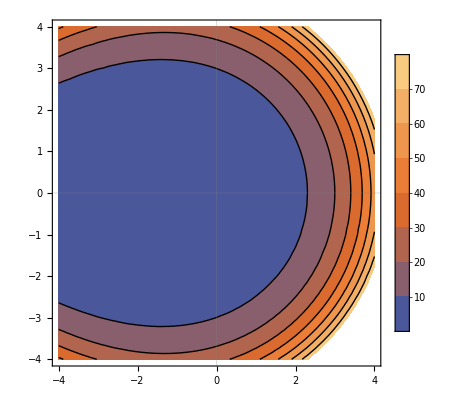

-Graphics3D-

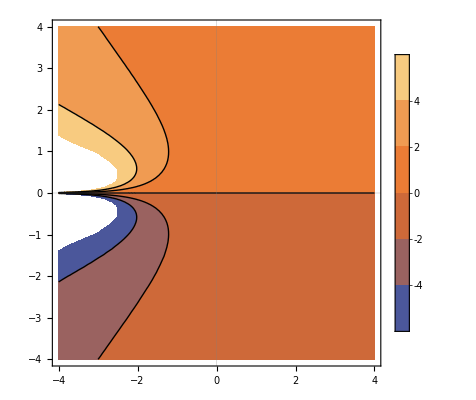

-Graphics3D-

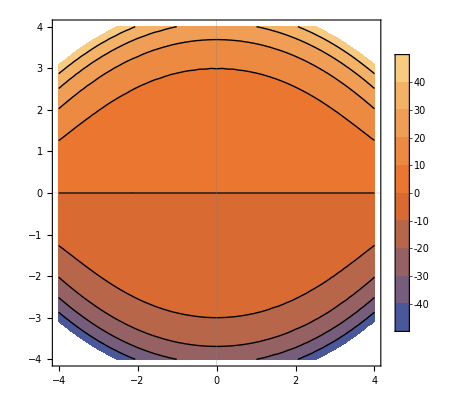

-Graphics3D-

```mathematica
ContourPlot[Cosh@√(x^2+y^2)+Cos@ArcTan[x,y]Sinh@√(x^2+y^2),{x,-4,4},{y,-4,4},PlotTheme->"Scientific",PlotLegends->Automatic]
Plot3D[Cosh@√(x^2+y^2)+Cos@ArcTan[x,y]Sinh@√(x^2+y^2),{x,-4,4},{y,-4,4},PlotTheme->"Scientific",PlotLegends->Automatic]
ContourPlot[(Sin@ArcTan[x,y]Sinh@√(x^2+y^2))/(Cosh@√(x^2+y^2)+Cos@ArcTan[x,y]Sinh@√(x^2+y^2)),{x,-4,4},{y,-4,4},PlotTheme->"Scientific",PlotLegends->Automatic]
Plot3D[(Sin@ArcTan[x,y]Sinh@√(x^2+y^2))/(Cosh@√(x^2+y^2)+Cos@ArcTan[x,y]Sinh@√(x^2+y^2)),{x,-4,4},{y,-4,4},PlotTheme->"Scientific",PlotLegends->Automatic]
ContourPlot[Sin@ArcTan[x,y]Sinh@√(x^2+y^2),{x,-4,4},{y,-4,4},PlotTheme->"Scientific",PlotLegends->Automatic]
Plot3D[Sin@ArcTan[x,y]Sinh@√(x^2+y^2),{x,-4,4},{y,-4,4},PlotTheme->"Scientific",PlotLegends->Automatic]
```

```mathematica
(*Double-mode squeezing*)
Integrate[1/(4π γ)^(1/2)ⅇ^(-(y-x)^2/(4γ))((m Ω)/π)^(1/4)ⅇ^(-(m Ω)/2 y^2) ,{y,-∞,∞},Assumptions->γ>0&&m>0&&Ω>0]
temp=FullSimplify[λ^(-1/2)ⅇ^(α x^2)(%/.x->x ⅇ^β)/.{α->ⅈ(m Ω)/2 σ,β->-Log[λ],γ->ⅈ 1/(2m Ω)σ},Assumptions->m>0&&Ω>0&&λ>0]
FullSimplify[ExpandAll[temp/.{λ->Cosh[r]+Cos[ϕ]Sinh[r],σ->(Sin[ϕ]Sinh[r])/(Cosh[r]+Cos[ϕ]Sinh[r])}]]; (*useless*)
FullSimplify[ExpandAll[(%/.x->xp)(%/.{x->xm,ϕ->ϕ+π})/.{xp->(x1+x2)/(√2),xm->(x1-x2)/(√2)}],Assumptions->m>0&&Ω>0&&r>0]
ClearAll[temp]
```

(ⅇ^(-(m x^2 Ω)/(2+4 m γ Ω)) (m Ω)^(1/4))/(π^(1/4) √(1+2 m γ Ω))

(ⅇ^(1/2 ⅈ m x^2 (σ+1/(λ^2 (-ⅈ+σ))) Ω) (m Ω)^(1/4))/(π^(1/4) √(λ+ⅈ λ σ))

(ⅇ^((m x^2 Ω (-Cosh[r-(ⅈ ϕ)/2]+Sinh[r+(ⅈ ϕ)/2]))/(2 (Cosh[r+(ⅈ ϕ)/2]+Sinh[r-(ⅈ ϕ)/2]))) (m Ω)^(1/4))/(π^(1/4) √(Cosh[r]+ⅇ^(ⅈ ϕ) Sinh[r]))

(ⅇ^(-(m Ω ((x1^2+x2^2) (Cos[ϕ] Cosh[2 r]-ⅈ Sin[ϕ])-2 x1 x2 Sinh[2 r]))/(2 (Cos[ϕ]-ⅈ Cosh[2 r] Sin[ϕ]))) √(m Ω))/(√π √(Cosh[r]^2-ⅇ^(2 ⅈ ϕ) Sinh[r]^2))

```mathematica
ComplexExpand[Cosh[r]^2-ⅇ^(2 ⅈ ϕ) Sinh[r]^2]
```

Cosh[r]^2-Cos[2 ϕ] Sinh[r]^2-ⅈ Sin[2 ϕ] Sinh[r]^2

```mathematica
-(m Ω (2 (x1^2+x2^2) Cosh[r]^2-8 ⅇ^(ⅈ ϕ) x1 x2 Cosh[r] Sinh[r]+2 ⅇ^(2 ⅈ ϕ) (x1^2+x2^2) Sinh[r]^2))/(-4 Cosh[r]^2+4 ⅇ^(2 ⅈ ϕ) Sinh[r]^2)
Coefficient[%,#]&/@{x1^2+x2^2,x1 x2}//Simplify
%/.Sinh[2r]->TrigExpand@Sinh[2r]/.{Cosh[r]->1,Sinh[r]->Tanh[r]}//FullSimplify
%(-2/(m Ω))//Simplify
%/.Tanh[r]->ⅇ^(-ⅈ ϕ)ⅇ^γ//ExpToTrig//FullSimplify
%/.γ->Log[β]//Simplify
```

-(m Ω (2 (x1^2+x2^2) Cosh[r]^2-8 ⅇ^(ⅈ ϕ) x1 x2 Cosh[r] Sinh[r]+2 ⅇ^(2 ⅈ ϕ) (x1^2+x2^2) Sinh[r]^2))/(-4 Cosh[r]^2+4 ⅇ^(2 ⅈ ϕ) Sinh[r]^2)

{(m Ω (Cosh[r]^2+ⅇ^(2 ⅈ ϕ) Sinh[r]^2))/(2 (Cosh[r]^2-ⅇ^(2 ⅈ ϕ) Sinh[r]^2)),(ⅇ^(ⅈ ϕ) m Ω Sinh[2 r])/(-Cosh[r]^2+ⅇ^(2 ⅈ ϕ) Sinh[r]^2)}

{(m Ω (1+ⅇ^(2 ⅈ ϕ) Tanh[r]^2))/(2-2 ⅇ^(2 ⅈ ϕ) Tanh[r]^2),(2 ⅇ^(ⅈ ϕ) m Ω Tanh[r])/(-1+ⅇ^(2 ⅈ ϕ) Tanh[r]^2)}

{(1+ⅇ^(2 ⅈ ϕ) Tanh[r]^2)/(-1+ⅇ^(2 ⅈ ϕ) Tanh[r]^2),-(4 ⅇ^(ⅈ ϕ) Tanh[r])/(-1+ⅇ^(2 ⅈ ϕ) Tanh[r]^2)}

{Coth[γ],-2 Csch[γ]}

{(1+β^2)/(-1+β^2),-(4 β)/(-1+β^2)}

```mathematica
{(1+β^2)/(1-β^2),(4 β)/(-1+β^2)}.{x1^2+x2^2,x1 x2};
FullSimplify[ComplexExpand[(%+(%*/.{x1->y1,x2->y2}))/.β->ⅇ^(ⅈ ϕ)Tanh[r],TargetFunctions->Conjugate],Assumptions->ϕ∈Reals&&r>0]
```

-((m Ω Sech[r]^4 (8 ⅇ^(2 ⅈ ϕ) (x1^2+x2^2+y1^2+y2^2) Cosh[2 r]+2 Sinh[2 r] (-4 (ⅇ^(ⅈ ϕ)+ⅇ^(3 ⅈ ϕ)) (x1 x2+y1 y2)-8 ⅈ ⅇ^(2 ⅈ ϕ) (x1 x2-y1 y2) Cosh[2 r] Sin[ϕ]+(-1+ⅇ^(4 ⅈ ϕ)) (x1^2+x2^2-y1^2-y2^2) Sinh[2 r])))/(16 (ⅇ^(2 ⅈ ϕ)-(1+ⅇ^(4 ⅈ ϕ)) Tanh[r]^2+ⅇ^(2 ⅈ ϕ) Tanh[r]^4)))

```mathematica
{(1+β^2)/(1-β^2),(4 β)/(-1+β^2)}.{x1^2+x2^2,x1 x2}
ComplexExpand[%*/.{x1->y1,x2->y2},β]//FullSimplify
FullSimplify[%%+%]
Collect[%/.{x1^2->x2s-x2^2,y1^2->y2s-y2^2}/.{x1->x12/x2,y1->y12/y2}//Simplify,{x2s,y2s,x12,y12}];
Coefficient[%,#]&/@{x2s,y2s,x12,y12}//Simplify//TraditionalForm
(*ComplexExpand[%,β,TargetFunctions->Conjugate]//FullSimplify*)
(m Ω)/π FullSimplify[(1-Abs[β]^2)/(√((1-β^2)(1-(β*)^2)))]Exp[-(m Ω)/2%%%]
Simplify[%/.{x1->x1+s1/2,y1->x1-s1/2,x2->x2+s2/2,y2->x2-s2/2},Assumptions->x1∈Reals&&x2∈Reals&&s1∈Reals&&s2∈Reals]
FullSimplify[FourierTransform[%,{s1,s2},{p1,p2}]/(2π),Assumptions->m>0&&Ω>0&&Abs[β]<1]
```

(4 x1 x2 β)/(-1+β^2)+((x1^2+x2^2) (1+β^2))/(1-β^2)

-(y1^2+y2^2-4 y1 y2 Conjugate[β]+(y1^2+y2^2) Conjugate[β]^2)/(-1+Conjugate[β]^2)

(4 x1 x2 β)/(-1+β^2)-((x1^2+x2^2) (1+β^2))/(-1+β^2)-(y1^2+y2^2-4 y1 y2 Conjugate[β]+(y1^2+y2^2) Conjugate[β]^2)/(-1+Conjugate[β]^2)

{(β^2+1)/(1-β^2),((Conjugate[β])^2+1)/(1-(Conjugate[β])^2),(4 β)/(β^2-1),(4 Conjugate[β])/((Conjugate[β])^2-1)}

(ⅇ^(-1/2 m Ω ((4 x1 x2 β)/(-1+β^2)-((x1^2+x2^2) (1+β^2))/(-1+β^2)-(y1^2+y2^2-4 y1 y2 Conjugate[β]+(y1^2+y2^2) Conjugate[β]^2)/(-1+Conjugate[β]^2))) m Ω (1-β Conjugate[β]))/(π √((-1+β^2) (-1+Conjugate[β]^2)))

-((ⅇ^(-1/2 m Ω (((s1+2 x1) (s2+2 x2) β)/(-1+β^2)-(((s1/2+x1)^2+(s2/2+x2)^2) (1+β^2))/(-1+β^2)-((-s1/2+x1)^2+(-s2/2+x2)^2-(s1-2 x1) (s2-2 x2) Conjugate[β]+((-s1/2+x1)^2+(-s2/2+x2)^2) Conjugate[β]^2)/(-1+Conjugate[β]^2))) m Ω (-1+β Conjugate[β]))/(π √((-1+β^2) (-1+Conjugate[β]^2))))

1/π^2 ⅇ^((p1^2+p2^2-4 ⅈ m (p2 x1+p1 x2) β Ω+m^2 (x1^2+x2^2) Ω^2+β (p1^2+p2^2+m^2 (x1^2+x2^2) Ω^2) Conjugate[β]+4 (p1+ⅈ m x1 Ω) (p2+ⅈ m x2 Ω) Re[β])/(m Ω (-1+Abs[β]^2))) √(1/((-1+β^2) (-1+Conjugate[β]^2))) √((-1+β^2) (-1+Conjugate[β]^2))

```mathematica
Coefficient[1/(m Ω (-1+Abs[β]^2))(p1^2+p2^2-4 ⅈ m (p2 x1+p1 x2) β Ω+m^2 (x1^2+x2^2) Ω^2+β (p1^2+p2^2+m^2 (x1^2+x2^2) Ω^2) Conjugate[β]+4 (p1+ⅈ m x1 Ω) (p2+ⅈ m x2 Ω) Re[β]),{x1^2,p1^2,x1 x2,x1 p2,p1 p2}]//Simplify
Simplify[%/.β->ⅇ^(ⅈ ϕ)tanhr//ComplexExpand,Assumptions->ϕ∈Reals&&tanhr>0&&tanhr<1]/.tanhr->Tanh[r]
%{(m Ω)^-1,(m Ω)^(+1),(m Ω)^-1,1,(m Ω)^(+1)}//FullSimplify
```

{(m Ω (1+β Conjugate[β]))/(-1+Abs[β]^2),-(1+β Conjugate[β])/(m Ω-m Ω Abs[β]^2),-(4 m Ω Re[β])/(-1+Abs[β]^2),-(4 ⅈ (β-Re[β]))/(-1+Abs[β]^2),-(4 Re[β])/(m Ω-m Ω Abs[β]^2)}

{(m Ω (1+Tanh[r]^2))/(-1+Tanh[r]^2),-(1+Tanh[r]^2)/(m Ω-m Ω Tanh[r]^2),-(4 m Ω Cos[ϕ] Tanh[r])/(-1+Tanh[r]^2),(4 Sin[ϕ] Tanh[r])/(-1+Tanh[r]^2),-(4 Cos[ϕ] Tanh[r])/(m Ω-m Ω Tanh[r]^2)}

{-Cosh[2 r],-Cosh[2 r],2 Cos[ϕ] Sinh[2 r],-2 Sin[ϕ] Sinh[2 r],-2 Cos[ϕ] Sinh[2 r]}